```mathematica
ClearAll
```

ClearAll

```mathematica
f1[x_]=b(4a^2+(x-z)^2+(x-z-a)Abs[x-z-a]-(x-z+a)Abs[x-z+a])
```

250000. (0.0004+(-0.5+x)^2+(-0.51+x) Abs[-0.51+x]-(-0.49+x) Abs[-0.49+x])

```mathematica
a=0.01;b=1/4/a/a/a;z=0.5;
```

```mathematica
Integrate[f1[x],{x,z-2a,z+2a}]
```

1.

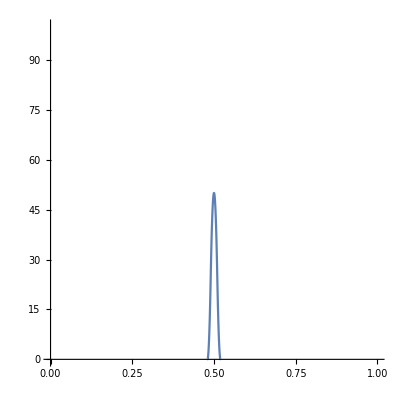

```mathematica
Plot[f1[x],{x,z-2a,z+2a},AspectRatio->1,PlotRange->{{0,1},{0,100}}]
```

```mathematica
Log[a,10]
```

-0.5

```mathematica
Clear[t,h]
```

```mathematica
b=1/h^5/24
```

1/(24 h^5)

```mathematica
f2[x_]=1/(24h^4)*Piecewise[{{(x-t)^4,t≤x≤t+h},{((x-t)^3(t+2h-x)+(x-t)^2(x-t-h)(t+3h-x)+(x-t)(x-t-h)^2(t+4h-x)+(x-t-h)^3(t+5h-x)),t+h≤x≤t+2h},{((x-t)^2(t+3h-x)^2+(x-t)(x-t-h)(t+3h-x)(t+4h-x)+(x-t)(x-t-2h)(t+4h-x)^2+(x-t-h)^2(t+3h-x)(t+5h-x)+(x-t-h)(x-t-2h)(t+4h-x)(t+5h-x)+(x-t-2h)^2(t+5h-x)^2),t+2h≤x≤t+3h},
{((x-t)(t+4h-x)^3+(x-t-h)(t+4h-x)^2(t+5h-x)+(x-t-2h)(t+4h-x)(t+5h-x)^2+(x-t-3h)(t+5h-x)^3),t+3h≤x≤t+4h},
{(t+5h-x)^4,t+4h≤x≤t+5h}},0]
```

1/(24 h^4)Piecewise[{{(-t+x)^4, t≤x≤h+t}, {(2 h+t-x) (-t+x)^3+(3 h+t-x) (-t+x)^2 (-h-t+x)+(4 h+t-x) (-t+x) (-h-t+x)^2+(5 h+t-x) (-h-t+x)^3, h+t≤x≤2 h+t}, {(3 h+t-x)^2 (-t+x)^2+(4 h+t-x)^2 (-t+x) (-2 h-t+x)+(5 h+t-x)^2 (-2 h-t+x)^2+(3 h+t-x) (4 h+t-x) (-t+x) (-h-t+x)+(4 h+t-x) (5 h+t-x) (-2 h-t+x) (-h-t+x)+(3 h+t-x) (5 h+t-x) (-h-t+x)^2, 2 h+t≤x≤3 h+t}, {(4 h+t-x)^3 (-t+x)+(5 h+t-x)^3 (-3 h-t+x)+(4 h+t-x) (5 h+t-x)^2 (-2 h-t+x)+(4 h+t-x)^2 (5 h+t-x) (-h-t+x), 3 h+t≤x≤4 h+t}, {(5 h+t-x)^4, 4 h+t≤x≤5 h+t}, {0, True}}]

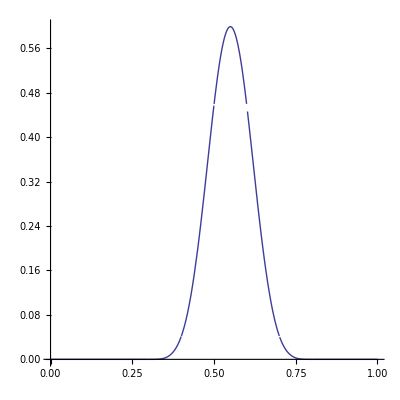

```mathematica
t=0.3;h=0.1;Plot[f2[x],{x,0,1},AspectRatio->1,PlotRange->Full]
```

```mathematica
Simplify[f2[x]]
```

416.667 (Piecewise[{{(-0.8+x)^4, 0.7<x≤0.8}, {(-0.3+x)^4, 0.3≤x≤0.4}, {-4. (0.197725-1.203 x+2.715 x^2-2.7 x^3+x^4), 0.6<x≤0.7}, {6. (0.0841833-0.638 x+1.79 x^2-2.2 x^3+x^4), 0.5<x≤0.6}, {-4. (0.029975-0.293 x+1.065 x^2-1.7 x^3+x^4), 0.4<x≤0.5}, {0, True}}])

```mathematica
g1[x_]=b*(x-t)^4
```

4166.67 (-0.3+x)^4

```mathematica
g2[x_]=b*((x-t)^3(t+2h-x)+(x-t)^2(x-t-h)(t+3h-x)+(x-t)(x-t-h)^2(t+4h-x)+(x-t-h)^3(t+5h-x))
```

4166.67 ((0.8-x) (-0.4+x)^3+(0.7-x) (-0.4+x)^2 (-0.3+x)+(0.6-x) (-0.4+x) (-0.3+x)^2+(0.5-x) (-0.3+x)^3)

```mathematica
g3[x_]=b*((x-t)^2(t+3h-x)^2+(x-t)(x-t-h)(t+3h-x)(t+4h-x)+(x-t)(x-t-2h)(t+4h-x)^2+(x-t-h)^2(t+3h-x)(t+5h-x)+(x-t-h)(x-t-2h)(t+4h-x)(t+5h-x)+(x-t-2h)^2(t+5h-x)^2)
```

4166.67 ((0.8-x)^2 (-0.5+x)^2+(0.7-x) (0.8-x) (-0.5+x) (-0.4+x)+(0.6-x) (0.8-x) (-0.4+x)^2+(0.7-x)^2 (-0.5+x) (-0.3+x)+(0.6-x) (0.7-x) (-0.4+x) (-0.3+x)+(0.6-x)^2 (-0.3+x)^2)

```mathematica
g4[x_]=b*((x-t)(t+4h-x)^3+(x-t-h)(t+4h-x)^2(t+5h-x)+(x-t-2h)(t+4h-x)(t+5h-x)^2+(x-t-3h)(t+5h-x)^3)
```

4166.67 ((0.8-x)^3 (-0.6+x)+(0.7-x) (0.8-x)^2 (-0.5+x)+(0.7-x)^2 (0.8-x) (-0.4+x)+(0.7-x)^3 (-0.3+x))

```mathematica
g5[x_]=b*(t+5h-x)^4
```

4166.67 (0.8-x)^4

```mathematica
Integrate[g1[x],{x,t,t+h}]+Integrate[g2[x],{x,t+h,t+2h}]+Integrate[g3[x],{x,t+2h,t+3h}]+Integrate[g4[x],{x,t+3h,t+4h}]+Integrate[g5[x],{x,t+4h,t+5h}]
```

1.

```mathematica
0==g1[t]
```

True

```mathematica
g1[t+h]==g2[t+h]
```

True

```mathematica
g2[t+2h]==g3[t+2h]
```

True

```mathematica
g3[t+3h]==g4[t+3h]
```

True

```mathematica
g4[t+4h]==g5[t+4h]
```

True

```mathematica
g5[t+5h]==0
```

True

```mathematica
f2p1[x_]=D[f2[x]]
```

416.667 (Piecewise[{{(-0.3+x)^4, 0.3≤x≤0.4}, {(0.8-x) (-0.4+x)^3+(0.7-x) (-0.4+x)^2 (-0.3+x)+(0.6-x) (-0.4+x) (-0.3+x)^2+(0.5-x) (-0.3+x)^3, 0.4≤x≤0.5}, {(0.8-x)^2 (-0.5+x)^2+(0.7-x) (0.8-x) (-0.5+x) (-0.4+x)+(0.6-x) (0.8-x) (-0.4+x)^2+(0.7-x)^2 (-0.5+x) (-0.3+x)+(0.6-x) (0.7-x) (-0.4+x) (-0.3+x)+(0.6-x)^2 (-0.3+x)^2, 0.5≤x≤0.6}, {(0.8-x)^3 (-0.6+x)+(0.7-x) (0.8-x)^2 (-0.5+x)+(0.7-x)^2 (0.8-x) (-0.4+x)+(0.7-x)^3 (-0.3+x), 0.6≤x≤0.7}, {(0.8-x)^4, 0.7≤x≤0.8}, {0, True}}])

```mathematica
t=0.3;h=0.1;Plot[f2p1[x],{x,0,1},AspectRatio->1,PlotRange->Full]
```

-Graphics-

```mathematica
Clear[t,h]
```

```mathematica
g1p1[x_]=D[g1[x],x];g2p1[x_]=D[g2[x],x];g3p1[x_]=D[g3[x],x];g4p1[x_]=D[g4[x],x];g5p1[x_]=D[g5[x],x];
```

```mathematica
0==g1p1[t]
```

0==16666.7 (-0.3+t)^3

```mathematica
g1p1[t+h]==g2p1[t+h]
```

16666.7 (-0.3+h+t)^3==4166.67 ((0.7-h-t) (-0.4+h+t)^2+3 (0.8-h-t) (-0.4+h+t)^2-(-0.4+h+t)^3+2 (0.6-h-t) (-0.4+h+t) (-0.3+h+t)+2 (0.7-h-t) (-0.4+h+t) (-0.3+h+t)-(-0.4+h+t)^2 (-0.3+h+t)+3 (0.5-h-t) (-0.3+h+t)^2+(0.6-h-t) (-0.3+h+t)^2-(-0.4+h+t) (-0.3+h+t)^2-(-0.3+h+t)^3)

```mathematica
g2p1[t+2h]==g3p1[t+2h]
```

4166.67 ((0.7-2 h-t) (-0.4+2 h+t)^2+3 (0.8-2 h-t) (-0.4+2 h+t)^2-(-0.4+2 h+t)^3+2 (0.6-2 h-t) (-0.4+2 h+t) (-0.3+2 h+t)+2 (0.7-2 h-t) (-0.4+2 h+t) (-0.3+2 h+t)-(-0.4+2 h+t)^2 (-0.3+2 h+t)+3 (0.5-2 h-t) (-0.3+2 h+t)^2+(0.6-2 h-t) (-0.3+2 h+t)^2-(-0.4+2 h+t) (-0.3+2 h+t)^2-(-0.3+2 h+t)^3)==4166.67 ((0.7-2 h-t)^2 (-0.5+2 h+t)+(0.7-2 h-t) (0.8-2 h-t) (-0.5+2 h+t)+2 (0.8-2 h-t)^2 (-0.5+2 h+t)-2 (0.8-2 h-t) (-0.5+2 h+t)^2+(0.6-2 h-t) (0.7-2 h-t) (-0.4+2 h+t)+2 (0.6-2 h-t) (0.8-2 h-t) (-0.4+2 h+t)+(0.7-2 h-t) (0.8-2 h-t) (-0.4+2 h+t)-(0.7-2 h-t) (-0.5+2 h+t) (-0.4+2 h+t)-(0.8-2 h-t) (-0.5+2 h+t) (-0.4+2 h+t)-(0.6-2 h-t) (-0.4+2 h+t)^2-(0.8-2 h-t) (-0.4+2 h+t)^2+2 (0.6-2 h-t)^2 (-0.3+2 h+t)+(0.6-2 h-t) (0.7-2 h-t) (-0.3+2 h+t)+(0.7-2 h-t)^2 (-0.3+2 h+t)-2 (0.7-2 h-t) (-0.5+2 h+t) (-0.3+2 h+t)-(0.6-2 h-t) (-0.4+2 h+t) (-0.3+2 h+t)-(0.7-2 h-t) (-0.4+2 h+t) (-0.3+2 h+t)-2 (0.6-2 h-t) (-0.3+2 h+t)^2)

```mathematica
g3p1[t+3h]==g4p1[t+3h]
```

4166.67 ((0.7-3 h-t)^2 (-0.5+3 h+t)+(0.7-3 h-t) (0.8-3 h-t) (-0.5+3 h+t)+2 (0.8-3 h-t)^2 (-0.5+3 h+t)-2 (0.8-3 h-t) (-0.5+3 h+t)^2+(0.6-3 h-t) (0.7-3 h-t) (-0.4+3 h+t)+2 (0.6-3 h-t) (0.8-3 h-t) (-0.4+3 h+t)+(0.7-3 h-t) (0.8-3 h-t) (-0.4+3 h+t)-(0.7-3 h-t) (-0.5+3 h+t) (-0.4+3 h+t)-(0.8-3 h-t) (-0.5+3 h+t) (-0.4+3 h+t)-(0.6-3 h-t) (-0.4+3 h+t)^2-(0.8-3 h-t) (-0.4+3 h+t)^2+2 (0.6-3 h-t)^2 (-0.3+3 h+t)+(0.6-3 h-t) (0.7-3 h-t) (-0.3+3 h+t)+(0.7-3 h-t)^2 (-0.3+3 h+t)-2 (0.7-3 h-t) (-0.5+3 h+t) (-0.3+3 h+t)-(0.6-3 h-t) (-0.4+3 h+t) (-0.3+3 h+t)-(0.7-3 h-t) (-0.4+3 h+t) (-0.3+3 h+t)-2 (0.6-3 h-t) (-0.3+3 h+t)^2)==4166.67 ((0.7-3 h-t)^3+(0.7-3 h-t)^2 (0.8-3 h-t)+(0.7-3 h-t) (0.8-3 h-t)^2+(0.8-3 h-t)^3-3 (0.8-3 h-t)^2 (-0.6+3 h+t)-2 (0.7-3 h-t) (0.8-3 h-t) (-0.5+3 h+t)-(0.8-3 h-t)^2 (-0.5+3 h+t)-(0.7-3 h-t)^2 (-0.4+3 h+t)-2 (0.7-3 h-t) (0.8-3 h-t) (-0.4+3 h+t)-3 (0.7-3 h-t)^2 (-0.3+3 h+t))

```mathematica
g4p1[t+4h]==g5p1[t+4h]
```

4166.67 ((0.7-4 h-t)^3+(0.7-4 h-t)^2 (0.8-4 h-t)+(0.7-4 h-t) (0.8-4 h-t)^2+(0.8-4 h-t)^3-3 (0.8-4 h-t)^2 (-0.6+4 h+t)-2 (0.7-4 h-t) (0.8-4 h-t) (-0.5+4 h+t)-(0.8-4 h-t)^2 (-0.5+4 h+t)-(0.7-4 h-t)^2 (-0.4+4 h+t)-2 (0.7-4 h-t) (0.8-4 h-t) (-0.4+4 h+t)-3 (0.7-4 h-t)^2 (-0.3+4 h+t))==-16666.7 (0.8-4 h-t)^3

```mathematica
g5p1[t+5h]==0
```

-16666.7 (0.8-5 h-t)^3==0

```mathematica
f2p2[x_]=D[f2p1[x]]
```

416.667 (Piecewise[{{(-0.3+x)^4, 0.3≤x≤0.4}, {(0.8-x) (-0.4+x)^3+(0.7-x) (-0.4+x)^2 (-0.3+x)+(0.6-x) (-0.4+x) (-0.3+x)^2+(0.5-x) (-0.3+x)^3, 0.4≤x≤0.5}, {(0.8-x)^2 (-0.5+x)^2+(0.7-x) (0.8-x) (-0.5+x) (-0.4+x)+(0.6-x) (0.8-x) (-0.4+x)^2+(0.7-x)^2 (-0.5+x) (-0.3+x)+(0.6-x) (0.7-x) (-0.4+x) (-0.3+x)+(0.6-x)^2 (-0.3+x)^2, 0.5≤x≤0.6}, {(0.8-x)^3 (-0.6+x)+(0.7-x) (0.8-x)^2 (-0.5+x)+(0.7-x)^2 (0.8-x) (-0.4+x)+(0.7-x)^3 (-0.3+x), 0.6≤x≤0.7}, {(0.8-x)^4, 0.7≤x≤0.8}, {0, True}}])

```mathematica
t=0.3;h=0.1;Plot[f2p2[x],{x,0,1},AspectRatio->1,PlotRange->Full]
```

-Graphics-

```mathematica
Clear[t,h]
```

```mathematica
g1p2[x_]=D[g1p1[x],x];g2p2[x_]=D[g2p1[x],x];g3p2[x_]=D[g3p1[x],x];g4p2[x_]=D[g4p1[x],x];g5p2[x_]=D[g5p1[x],x];
```

```mathematica
0==g1p2[t]
```

0==50000. (-0.3+t)^2

```mathematica
g1p2[t+h]==g2p2[t+h]
```

50000. (-0.3+h+t)^2==4166.67 (2 (0.6-h-t) (-0.4+h+t)+4 (0.7-h-t) (-0.4+h+t)+6 (0.8-h-t) (-0.4+h+t)-8 (-0.4+h+t)^2+6 (0.5-h-t) (-0.3+h+t)+4 (0.6-h-t) (-0.3+h+t)+2 (0.7-h-t) (-0.3+h+t)-8 (-0.4+h+t) (-0.3+h+t)-8 (-0.3+h+t)^2)

```mathematica
g2p2[t+2h]==g3p2[t+2h]
```

4166.67 (2 (0.6-2 h-t) (-0.4+2 h+t)+4 (0.7-2 h-t) (-0.4+2 h+t)+6 (0.8-2 h-t) (-0.4+2 h+t)-8 (-0.4+2 h+t)^2+6 (0.5-2 h-t) (-0.3+2 h+t)+4 (0.6-2 h-t) (-0.3+2 h+t)+2 (0.7-2 h-t) (-0.3+2 h+t)-8 (-0.4+2 h+t) (-0.3+2 h+t)-8 (-0.3+2 h+t)^2)==4166.67 (2 (0.6-2 h-t)^2+2 (0.6-2 h-t) (0.7-2 h-t)+2 (0.7-2 h-t)^2+2 (0.6-2 h-t) (0.8-2 h-t)+2 (0.7-2 h-t) (0.8-2 h-t)+2 (0.8-2 h-t)^2-6 (0.7-2 h-t) (-0.5+2 h+t)-10 (0.8-2 h-t) (-0.5+2 h+t)+2 (-0.5+2 h+t)^2-6 (0.6-2 h-t) (-0.4+2 h+t)-4 (0.7-2 h-t) (-0.4+2 h+t)-6 (0.8-2 h-t) (-0.4+2 h+t)+2 (-0.5+2 h+t) (-0.4+2 h+t)+2 (-0.4+2 h+t)^2-10 (0.6-2 h-t) (-0.3+2 h+t)-6 (0.7-2 h-t) (-0.3+2 h+t)+2 (-0.5+2 h+t) (-0.3+2 h+t)+2 (-0.4+2 h+t) (-0.3+2 h+t)+2 (-0.3+2 h+t)^2)

```mathematica
g3p2[t+3h]==g4p2[t+3h]
```

4166.67 (2 (0.6-3 h-t)^2+2 (0.6-3 h-t) (0.7-3 h-t)+2 (0.7-3 h-t)^2+2 (0.6-3 h-t) (0.8-3 h-t)+2 (0.7-3 h-t) (0.8-3 h-t)+2 (0.8-3 h-t)^2-6 (0.7-3 h-t) (-0.5+3 h+t)-10 (0.8-3 h-t) (-0.5+3 h+t)+2 (-0.5+3 h+t)^2-6 (0.6-3 h-t) (-0.4+3 h+t)-4 (0.7-3 h-t) (-0.4+3 h+t)-6 (0.8-3 h-t) (-0.4+3 h+t)+2 (-0.5+3 h+t) (-0.4+3 h+t)+2 (-0.4+3 h+t)^2-10 (0.6-3 h-t) (-0.3+3 h+t)-6 (0.7-3 h-t) (-0.3+3 h+t)+2 (-0.5+3 h+t) (-0.3+3 h+t)+2 (-0.4+3 h+t) (-0.3+3 h+t)+2 (-0.3+3 h+t)^2)==4166.67 (-8 (0.7-3 h-t)^2-8 (0.7-3 h-t) (0.8-3 h-t)-8 (0.8-3 h-t)^2+6 (0.8-3 h-t) (-0.6+3 h+t)+2 (0.7-3 h-t) (-0.5+3 h+t)+4 (0.8-3 h-t) (-0.5+3 h+t)+4 (0.7-3 h-t) (-0.4+3 h+t)+2 (0.8-3 h-t) (-0.4+3 h+t)+6 (0.7-3 h-t) (-0.3+3 h+t))

```mathematica
g4p2[t+4h]==g5p2[t+4h]
```

4166.67 (-8 (0.7-4 h-t)^2-8 (0.7-4 h-t) (0.8-4 h-t)-8 (0.8-4 h-t)^2+6 (0.8-4 h-t) (-0.6+4 h+t)+2 (0.7-4 h-t) (-0.5+4 h+t)+4 (0.8-4 h-t) (-0.5+4 h+t)+4 (0.7-4 h-t) (-0.4+4 h+t)+2 (0.8-4 h-t) (-0.4+4 h+t)+6 (0.7-4 h-t) (-0.3+4 h+t))==50000. (0.8-4 h-t)^2

```mathematica
g5p2[t+5h]==0
```

50000. (0.8-5 h-t)^2==0

```mathematica
f2p3[x_]=D[f2p2[x]]
```

416.667 (Piecewise[{{(-0.3+x)^4, 0.3≤x≤0.4}, {(0.8-x) (-0.4+x)^3+(0.7-x) (-0.4+x)^2 (-0.3+x)+(0.6-x) (-0.4+x) (-0.3+x)^2+(0.5-x) (-0.3+x)^3, 0.4≤x≤0.5}, {(0.8-x)^2 (-0.5+x)^2+(0.7-x) (0.8-x) (-0.5+x) (-0.4+x)+(0.6-x) (0.8-x) (-0.4+x)^2+(0.7-x)^2 (-0.5+x) (-0.3+x)+(0.6-x) (0.7-x) (-0.4+x) (-0.3+x)+(0.6-x)^2 (-0.3+x)^2, 0.5≤x≤0.6}, {(0.8-x)^3 (-0.6+x)+(0.7-x) (0.8-x)^2 (-0.5+x)+(0.7-x)^2 (0.8-x) (-0.4+x)+(0.7-x)^3 (-0.3+x), 0.6≤x≤0.7}, {(0.8-x)^4, 0.7≤x≤0.8}, {0, True}}])

```mathematica
t=0.3;h=0.1;Plot[f2p3[x],{x,0,1},AspectRatio->1,PlotRange->Full]
```

-Graphics-

```mathematica
Clear[t,h]
```